# Jakub Pietrasik, Bartosz Lewandowicz, Szymon Hankus Mathematical and computer modeling of various technical and scientific problems - Final Project

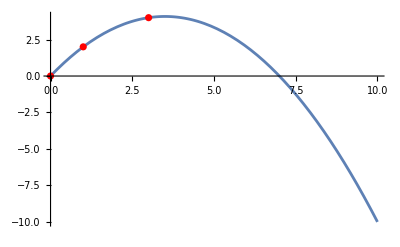

```mathematica
Lagrange[points_List]:=Module[{w, n,  i, phi, k},
w= 0;
n = Length[points];

For[i = 1, i <= n, i++,
phi = 1;

For[k = 1, k <= n, k++,
If[k!=i, phi =phi* (x-points⟦k,1⟧)/(points⟦i,1⟧-points⟦k,1⟧)];
];
w= w + points⟦i,2⟧*phi;
];

Return[w];
]

points={{0,0},{1,2},{3,4}};
Show[
Plot[Lagrange[points],{x,0,10}],
ListPlot[points, PlotStyle->Red]
]
```

```mathematica
f[x_]:=1-x^2

calculateCoefficient[f_,n_,x_,period_,type_]:=Module[{integrand},integrand=f*If[type=="Cos",Cos[2 Pi n x/period],Sin[2 Pi n x/period]];
(2/period) Integrate[integrand,{x,-period/2,period/2}]];

fourierCoefficients[f_,n_,x_,period_]:=Module[{a0,an,bn},a0=(1/period) Integrate[f,{x,-period/2,period/2}];
an=Table[calculateCoefficient[f,m,x,period,"Cos"],{m,1,n}];
bn=Table[calculateCoefficient[f,m,x,period,"Sin"],{m,1,n}];
{a0}~Join~an~Join~bn];

fourierSeries[x_,n_,period_]:=Module[{coefficients,terms},coefficients=fourierCoefficients[f[x],n,x,period];
terms=Table[coefficients[[m+1]] Cos[2 Pi m x/period]+coefficients[[n+m+1]] Sin[2 Pi m x/period],{m,0,n}];
Total[terms]];

Manipulate[Module[{approximation,plotRange},approximation=fourierSeries[x,n,2 Pi];
Plot[{f[x],approximation},{x,-Pi,Pi},PlotRange->{{-Pi,Pi},Automatic},PlotStyle->{Red,Blue},Epilog->{Text["Original Function",{Pi/2,1.2}],Text["Fourier Series Approximation",{Pi/2,-0.2}]},AxesLabel->{"x","y"},PlotLegends->{"Original Function","Fourier Series Approximation"},ImageSize->400]],{{n,1,"Number of Terms"},1,20,1,Appearance->"Labeled"}]
```